# Quantum Corrections to Symmetron Fifth-Force Profiles

```mathematica
ClearAll["Global`*"]
```

## Initialisation

### Parameters

```mathematica
primaryParams = {μ->10^-6,ρ0->Rationalize[(938 10^-3)/(4/3 π (0.877 10^-15)^3 (1/0.197 10^15)^3)] ,M->10^4,λ->0.5}; (* input parameters *)
secondaryParams = {γ->μ/(√2), g-> √(2(ρ0/(μ^2 M^2)-1)),v-> μ/(√λ)}; (* derived from input parameters *)
tertiaryParams = {χ0->1/(√(2+g^2)), u0 -> 1/(√(2+g^2)), z0 -> 1/(g^2 (2 + g^2))}; (* derived from secondary parameters *)
allParams = Flatten[{tertiaryParams/.secondaryParams/.primaryParams,secondaryParams/.primaryParams, primaryParams}]
```

{χ0→0.140355,u0→0.140355,z0→0.000403988,γ→1/(1000000 √2),g→6.98302,v→1.41421×10^-6,μ→1/1000000,ρ0→0.00253813,M→10000,λ→0.5}

```mathematica
n[p_] := 1/γ √(p^2 + 4 γ^2)/.allParams;
α[p_]:=1/(2 g) √(n[p]^2 - 4 + g^2)/.allParams;
```

### Functions

```mathematica
Θ[s_]:=Piecewise[{{0, s<0}, {1/2, s == 0}, {1, s> 0}}] (*faster step function*);
ρ[s_]:= ρ0 UnitStep[-s] (*density distributions*);
P[μ_, x_]:=(((1+x)/(1-x))^(μ/2) (-1+3 x^2-3 x μ+μ^2))/Gamma[3-μ] (*exterior eigenmode*);
F[α_, z_]:= (2^(-1+2 α) z^α (1+√(1+z))^(-2 α) (2+3 z+6 √(1+z) α+4 α^2))/(1+3 α+2 α^2) (*interior eigenmode*);
u[s_]:=Tanh[γ s + ArcTanh[χ0]] (*exterior substitution*);
z[s_] := Csch[ArcCsch[χ0/g] - g γ s]^2 (*interior substitution*);
χExt[s_]:=Tanh[γ s + ArcTanh[χ0]] (*exterior normalised field*);
χInt[s_]:=g Csch[ArcCsch[χ0/g]-g γ s] (*interior normalised field*);
χ[s_]:=χInt[s] Θ[-s] + χExt[s] Θ[s] (*full normalised field*);
```

## Green’s Functions

### Wronskians

```mathematica
WronskianFast[{f_, g_}, x_] := f D[g , x]- g D[f, x] (*faster Wronskian function*);
```

```mathematica
WPlus= Simplify[WronskianFast[{P[n[p], u[s]], F[α[p], z[s]]}, s]/. s->0, Assumptions->p>0] (*occurs in G_(++)*);
WMinus=Simplify[WronskianFast[{P[-n[p], u[s]], F[-α[p], z[s]]}, s]/.s->0, Assumptions->p>0] (*occurs in G_(--)*);
W= Simplify[WronskianFast[{F[α[p], z[s]], P[-n[p], u[s]]}, s]/.s->0, Assumptions->p>0] (*occurs in every contribution*);
```

### Field-Space Definitions

#### Nonzero momentum

```mathematica
(*FullSimplify[FunctionExpand[-π/(2 γ) Csc[n[p] π] P[-n[p], x] P[n[p], y]]]*) (*gives the below expression*)
```

```mathematica
GPlus1[x_, y_]:= Evaluate[(((1+x)/(1-x))^(-(√(p^2+4 γ^2))/(2 γ)) ((1+y)/(1-y))^((√(p^2+4 γ^2))/(2 γ)) (p^2+3 γ (γ+x^2 γ+x √(p^2+4 γ^2))) (-p^2-3 γ (γ+y^2 γ-y √(p^2+4 γ^2))))/(2 p^2 (p^2+3 γ^2) √(p^2+4 γ^2))]
```

```mathematica
(*FullSimplify[FunctionExpand[-π/(2 γ) Csc[n[p] π] P[-n[p], x] P[-n[p], y]] WPlus/W]*) (*And another FunctionExpand on the product of gamma functions afterwards*)
```

```mathematica
GPlus2[x_, y_]:= Evaluate[(((1+x)/(1-x))^(-(√(p^2+4 γ^2))/(2 γ)) ((1+y)/(1-y))^(-(√(p^2+4 γ^2))/(2 γ)) (p^2+3 γ (γ+x^2 γ+x √(p^2+4 γ^2))) (p^2+3 γ (γ+y^2 γ+y √(p^2+4 γ^2))) ((1+χ0)/(1-χ0))^((√(p^2+4 γ^2))/γ) (-g^3 (-1+χ0^2) √(1+χ0^2/g^2) (1+√(1+χ0^2/g^2))^(-(√(g^2+p^2/γ^2))/g) (-p^2 (√(p^2+4 γ^2)-3 γ χ0)+6 γ^2 χ0 (γ-√(p^2+4 γ^2) χ0+γ χ0^2)) (p^2+3 γ^2 (g^2+χ0^2+g √(g^2+p^2/γ^2) √(1+χ0^2/g^2)))-√(1+g^2/χ0^2) (-1+χ0) (1+χ0) (1+√(1+χ0^2/g^2))^(-1-(√(g^2+p^2/γ^2))/g) (p^2+3 γ (γ-√(p^2+4 γ^2) χ0+γ χ0^2)) (3 g γ χ0^3 (p^2+2 γ^2 χ0^2)+3 g^5 γ^3 χ0 (1+√(1+χ0^2/g^2))+3 g^4 √(g^2+p^2/γ^2) γ^3 χ0 (1+√(1+χ0^2/g^2))+g^2 √(g^2+p^2/γ^2) γ χ0 (p^2+6 γ^2 χ0^2) (1+√(1+χ0^2/g^2))+g^3 (3 p^2 γ χ0 (1+√(1+χ0^2/g^2))+3 γ^3 χ0^3 (3+2 √(1+χ0^2/g^2))))))/(2 √(p^2+4 γ^2) (-2 γ+√(p^2+4 γ^2)) (-γ+√(p^2+4 γ^2)) (γ+√(p^2+4 γ^2)) (2 γ+√(p^2+4 γ^2)) (-g^3 (-1+χ0^2) √(1+χ0^2/g^2) (1+√(1+χ0^2/g^2))^(-(√(g^2+p^2/γ^2))/g) (p^2 (√(p^2+4 γ^2)+3 γ χ0)+6 γ^2 χ0 (γ+√(p^2+4 γ^2) χ0+γ χ0^2)) (p^2+3 γ^2 (g^2+χ0^2+g √(g^2+p^2/γ^2) √(1+χ0^2/g^2)))-√(1+g^2/χ0^2) (-1+χ0) (1+χ0) (1+√(1+χ0^2/g^2))^(-1-(√(g^2+p^2/γ^2))/g) (p^2+3 γ (γ+√(p^2+4 γ^2) χ0+γ χ0^2)) (3 g γ χ0^3 (p^2+2 γ^2 χ0^2)+3 g^5 γ^3 χ0 (1+√(1+χ0^2/g^2))+3 g^4 √(g^2+p^2/γ^2) γ^3 χ0 (1+√(1+χ0^2/g^2))+g^2 √(g^2+p^2/γ^2) γ χ0 (p^2+6 γ^2 χ0^2) (1+√(1+χ0^2/g^2))+g^3 (3 p^2 γ χ0 (1+√(1+χ0^2/g^2))+3 γ^3 χ0^3 (3+2 √(1+χ0^2/g^2))))))];
```

```mathematica
(*FullSimplify[FunctionExpand[- 1/(4 α[p] g γ) F[α[p],y^2/g^2]F[-α[p], x^2/g^2]]]*)
```

```mathematica
GMinus1[x_, y_]:=-1/(2 √(g^2+p^2/γ^2) (-p^4 γ+3 g^2 p^2 γ^3))(x^2/g^2)^(-(√(g^2+p^2/γ^2))/(2 g)) (1+√(1+x^2/g^2))^((√(g^2+p^2/γ^2))/g) (y^2/g^2)^((√(g^2+p^2/γ^2))/(2 g)) (1+√(1+y^2/g^2))^(-(√(g^2+p^2/γ^2))/g) (p^2+3 (g^2+y^2+g √(1+y^2/g^2) √(g^2+p^2/γ^2)) γ^2) (-p^2-3 g^2 γ^2-3 x^2 γ^2+3 g √(1+x^2/g^2) √(g^2+p^2/γ^2) γ^2);
```

```mathematica
(*FullSimplify[FunctionExpand[- 1/(4 α[p] g γ) F[α[p],y^2/g^2] WMinus/W F[α[p], x^2/g^2]]]*)
```

```mathematica
GMinus2[x_, y_]:=((x^2/g^2)^((√(g^2+p^2/γ^2))/(2 g)) (1+√(1+x^2/g^2))^(-(√(g^2+p^2/γ^2))/g) (y^2/g^2)^((√(g^2+p^2/γ^2))/(2 g)) (1+√(1+y^2/g^2))^(-(√(g^2+p^2/γ^2))/g) (p^2+3 (g^2+x^2+g √(1+x^2/g^2) √(g^2+p^2/γ^2)) γ^2) (p^2+3 (g^2+y^2+g √(1+y^2/g^2) √(g^2+p^2/γ^2)) γ^2) (χ0^2/g^2)^(-(√(g^2+p^2/γ^2))/g) (-g^3 (-1+χ0^2) √(1+χ0^2/g^2) (1+√(1+χ0^2/g^2))^((√(g^2+p^2/γ^2))/g) (-p^2-3 g^2 γ^2-3 γ^2 χ0^2+3 g √(g^2+p^2/γ^2) γ^2 √(1+χ0^2/g^2)) (p^2 (√(p^2+4 γ^2)+3 γ χ0)+6 γ^2 χ0 (γ+√(p^2+4 γ^2) χ0+γ χ0^2))+g γ √(1+g^2/χ0^2) χ0 (-1+χ0^2) (1+√(1+χ0^2/g^2))^(-1+(√(g^2+p^2/γ^2))/g) (p^2+3 γ (γ+√(p^2+4 γ^2) χ0+γ χ0^2)) (3 χ0^2 (p^2+2 γ^2 χ0^2)+3 g^4 γ^2 (1+√(1+χ0^2/g^2))-3 g^3 √(g^2+p^2/γ^2) γ^2 (1+√(1+χ0^2/g^2))-g √(g^2+p^2/γ^2) (p^2+6 γ^2 χ0^2) (1+√(1+χ0^2/g^2))+3 g^2 (p^2 (1+√(1+χ0^2/g^2))+γ^2 χ0^2 (3+2 √(1+χ0^2/g^2))))))/(2 √(g^2+p^2/γ^2) γ (p^2+3 g (g-√(g^2+p^2/γ^2)) γ^2) (p^2+3 g (g+√(g^2+p^2/γ^2)) γ^2) (g^3 (-1+χ0^2) √(1+χ0^2/g^2) (1+√(1+χ0^2/g^2))^(-(√(g^2+p^2/γ^2))/g) (p^2 (√(p^2+4 γ^2)+3 γ χ0)+6 γ^2 χ0 (γ+√(p^2+4 γ^2) χ0+γ χ0^2)) (p^2+3 γ^2 (g^2+χ0^2+g √(g^2+p^2/γ^2) √(1+χ0^2/g^2)))+g γ √(1+g^2/χ0^2) χ0 (-1+χ0^2) (1+√(1+χ0^2/g^2))^(-1-(√(g^2+p^2/γ^2))/g) (p^2+3 γ (γ+√(p^2+4 γ^2) χ0+γ χ0^2)) (3 χ0^2 (p^2+2 γ^2 χ0^2)+3 g^4 γ^2 (1+√(1+χ0^2/g^2))+3 g^3 √(g^2+p^2/γ^2) γ^2 (1+√(1+χ0^2/g^2))+g √(g^2+p^2/γ^2) (p^2+6 γ^2 χ0^2) (1+√(1+χ0^2/g^2))+3 g^2 (p^2 (1+√(1+χ0^2/g^2))+γ^2 χ0^2 (3+2 √(1+χ0^2/g^2))))));
```

```mathematica
GPlusField[x_, y_]:= GPlus1[x, y] + GPlus2[x, y]
```

```mathematica
GMinusField[x_, y_]:=GMinus1[x, y] + GMinus2[x, y]
```

```mathematica
GMixedField[x_, y_]:= (F[α[p], y^2/g^2] P[-n[p], x])/W;
```

```mathematica
GgtrField[x_, y_]:= Θ[x - χ0] Θ[y-χ0] GPlusField[x, y]+ Θ[x-χ0] Θ[χ0-y] GMixedField[x, y]+ Θ[χ0-x] Θ[χ0-y] GMinusField[x, y]
```

```mathematica
GField[x_, y_]:=Θ[y - x] GgtrField[y, x] + Θ[x - y] GgtrField[x, y]
```

#### Zero momentum

```mathematica
(*Limit[GPlusField[x, y], p->0, Assumptions->γ>0&&g>0]*)
```

```mathematica
GPlusFieldRest[x_, y_]:=((-1+x) (1+y) (-5+3 x^2-20 x y-16 x^2 y+3 y^2+16 x y^2+11 x^2 y^2+3 (1+x)^2 (-1+y)^2 Log[-(1+x)/(-1+x)]-3 (1+x)^2 (-1+y)^2 Log[-(1+y)/(-1+y)]))/(32 (1+x) (-1+y) γ)+1/2 (-((3 (1-x) (1-y) (γ+2 x γ+x^2 γ) (γ+2 y γ+y^2 γ) (1+χ0)^2 (-(18 g^2 γ^5 (-1+χ0)^3 χ0 (1+χ0) √(g^2+χ0^2) (g^2+χ0^2+g √(g^2+χ0^2)))/(1+(√(g^2+χ0^2))/g)-(9 γ^5 (-1+χ0)^3 (1+χ0) √((g^2+χ0^2)/χ0^2) (2 g^5 χ0+5 g^3 χ0^3+2 g χ0^5+2 g^4 χ0 √(g^2+χ0^2)+4 g^2 χ0^3 √(g^2+χ0^2)))/((1+(√(g^2+χ0^2))/g)^2)) (√(1+g^2/χ0^2) (-1+χ0) (1+χ0) (-(3 γ (γ+2 γ χ0+γ χ0^2) (3 g γ χ0^3+g γ χ0 (g^2+3 χ0^2) (1+(√(g^2+χ0^2))/g)+9/2 g^3 γ χ0 (1+√(1+χ0^2/g^2))))/((1+√(1+χ0^2/g^2))^2)-3 (2 g^5 γ^3 χ0+5 g^3 γ^3 χ0^3+2 g γ^3 χ0^5+2 g^4 γ^3 χ0 √(g^2+χ0^2)+4 g^2 γ^3 χ0^3 √(g^2+χ0^2)) ((1+(3 χ0)/4)/((1+√(1+χ0^2/g^2))^2)-(3 (γ+2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(2 g^2 γ (1+√(1+χ0^2/g^2))^2)))+g^3 (-1+χ0^2) √(1+χ0^2/g^2) (-(6 γ^2 χ0 (γ+2 γ χ0+γ χ0^2) (1+3/2 √(1+χ0^2/g^2)))/(1+√(1+χ0^2/g^2))-3 γ^2 (g^2+χ0^2+g^2 √(1+χ0^2/g^2)) ((2 γ+3 γ χ0+(3 γ χ0^2)/2)/(1+√(1+χ0^2/g^2))-(3 χ0 (γ+2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(g^2 (1+√(1+χ0^2/g^2)))))))/(2 (1+x) (1+y) γ (-1+χ0)^2 (-(18 g^2 γ^5 (-1+χ0) χ0 (1+χ0)^3 √(g^2+χ0^2) (g^2+χ0^2+g √(g^2+χ0^2)))/(1+(√(g^2+χ0^2))/g)-(9 γ^5 (-1+χ0) (1+χ0)^3 √((g^2+χ0^2)/χ0^2) (2 g^5 χ0+5 g^3 χ0^3+2 g χ0^5+2 g^4 χ0 √(g^2+χ0^2)+4 g^2 χ0^3 √(g^2+χ0^2)))/((1+(√(g^2+χ0^2))/g)^2))^2))+((-(18 g^2 γ^5 (-1+χ0)^3 χ0 (1+χ0) √(g^2+χ0^2) (g^2+χ0^2+g √(g^2+χ0^2)))/(1+(√(g^2+χ0^2))/g)-(9 γ^5 (-1+χ0)^3 (1+χ0) √((g^2+χ0^2)/χ0^2) (2 g^5 χ0+5 g^3 χ0^3+2 g χ0^5+2 g^4 χ0 √(g^2+χ0^2)+4 g^2 χ0^3 √(g^2+χ0^2)))/((1+(√(g^2+χ0^2))/g)^2)) (1/(-1+χ0)^2(1+χ0)^2 (((1-x) (1-y) (1+(3 y)/4) (γ+2 x γ+x^2 γ))/(2 (1+x) (1+y) γ^2)+3 γ (γ+2 y γ+y^2 γ) (((1-x) (1+(3 x)/4) (1-y))/(6 (1+x) (1+y) γ^3)+3 γ (γ+2 x γ+x^2 γ) (-((1-x) (1-y))/(96 (1+x) (1+y) γ^5)+(-((1-x) (1-y))/(18 (1+x) (1+y) γ^4)+(-((1-x) (1-y))/(2 (1+x) (1+y) γ^3)+(((1-x) (1-y))/(8 (1+x) (1+y) γ^2)+4 γ (-((1-x) (1-y))/(16 (1+x) (1+y) γ^3)+(((-1+x) (1-y) Log[(1+x)/(1-x)])/(8 (1+x) (1+y) γ^2)+((1-x) (-1+y) Log[(1+y)/(1-y)])/(8 (1+x) (1+y) γ^2))/(2 γ)))/γ)/(3 γ))/(4 γ))))+(3 (1-x) (1-y) (γ+2 x γ+x^2 γ) (γ+2 y γ+y^2 γ) (1+χ0)^2 Log[(1+χ0)/(1-χ0)])/(8 (1+x) (1+y) γ^3 (-1+χ0)^2))+1/(2 (1+x) (1+y) γ (-1+χ0)^2)3 (1-x) (1-y) (γ+2 x γ+x^2 γ) (γ+2 y γ+y^2 γ) (1+χ0)^2 (√(1+g^2/χ0^2) (-1+χ0) (1+χ0) (-(3 γ (γ-2 γ χ0+γ χ0^2) (3 g γ χ0^3+g γ χ0 (g^2+3 χ0^2) (1+(√(g^2+χ0^2))/g)+9/2 g^3 γ χ0 (1+√(1+χ0^2/g^2))))/((1+√(1+χ0^2/g^2))^2)-3 (2 g^5 γ^3 χ0+5 g^3 γ^3 χ0^3+2 g γ^3 χ0^5+2 g^4 γ^3 χ0 √(g^2+χ0^2)+4 g^2 γ^3 χ0^3 √(g^2+χ0^2)) ((1-(3 χ0)/4)/((1+√(1+χ0^2/g^2))^2)-(3 (γ-2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(2 g^2 γ (1+√(1+χ0^2/g^2))^2)))+g^3 (-1+χ0^2) √(1+χ0^2/g^2) (-(6 γ^2 χ0 (γ-2 γ χ0+γ χ0^2) (1+3/2 √(1+χ0^2/g^2)))/(1+√(1+χ0^2/g^2))-3 γ^2 (g^2+χ0^2+g^2 √(1+χ0^2/g^2)) ((-2 γ+3 γ χ0-(3 γ χ0^2)/2)/(1+√(1+χ0^2/g^2))-(3 χ0 (γ-2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(g^2 (1+√(1+χ0^2/g^2)))))))/(-(18 g^2 γ^5 (-1+χ0) χ0 (1+χ0)^3 √(g^2+χ0^2) (g^2+χ0^2+g √(g^2+χ0^2)))/(1+(√(g^2+χ0^2))/g)-(9 γ^5 (-1+χ0) (1+χ0)^3 √((g^2+χ0^2)/χ0^2) (2 g^5 χ0+5 g^3 χ0^3+2 g χ0^5+2 g^4 χ0 √(g^2+χ0^2)+4 g^2 χ0^3 √(g^2+χ0^2)))/((1+(√(g^2+χ0^2))/g)^2)));
```

```mathematica
(*Limit[GMinusField[x, y], p->0, Assumptions->γ>0&&g>0]*)
```

```mathematica
GMinusFieldRest[x_, y_] := 1/2 (-((1+(√(g^2+x^2))/g) √(y^2) (1+(3 √(g^2+y^2))/(2 g)) (-3 g^2 γ^2-3 x^2 γ^2+3 g √(g^2+x^2) γ^2))/(3 g^3 √(x^2) (1+(√(g^2+y^2))/g) γ^3)+3 (g^2 γ^2+y^2 γ^2+g √(g^2+y^2) γ^2) (-((1+(√(g^2+x^2))/g) (-1+(3 √(g^2+x^2))/(2 g)) √(y^2))/(3 g^3 √(x^2) (1+(√(g^2+y^2))/g) γ^3)+(-3 g^2 γ^2-3 x^2 γ^2+3 g √(g^2+x^2) γ^2) (((1+(√(g^2+x^2))/g) √(y^2))/(6 g^5 √(x^2) (1+(√(g^2+y^2))/g) γ^5)+(-((1+(√(g^2+x^2))/g) √(y^2))/(9 g^4 √(x^2) (1+(√(g^2+y^2))/g) γ^4)-((√(y^2) (-((1+(√(g^2+x^2))/g) Log[x^2])/(4 g^2 √(x^2) γ^2)+((g+√(g^2+x^2)) Log[1+(√(g^2+x^2))/g])/(2 g^3 √(x^2) γ^2))+((1+(√(g^2+x^2))/g) √(y^2) Log[y^2])/(4 g^2 √(x^2) γ^2))/(1+(√(g^2+y^2))/g)-((1+(√(g^2+x^2))/g) √(y^2) Log[1+(√(g^2+y^2))/g])/(2 g √(x^2) (g+√(g^2+y^2)) γ^2))/(3 g^2 γ^2))/(g γ))))+1/(2 γ)((27 √(x^2) (g^2+x^2+g^2 √(1+x^2/g^2)) √(y^2) (g^2+y^2+g^2 √(1+y^2/g^2)) γ^7 (-1+χ0) (1+χ0)^3 (2 g^3 χ0^2+2 g χ0^4+g^3 χ0^2 √((g^2+χ0^2)/χ0^2)+2 g χ0^4 √((g^2+χ0^2)/χ0^2)) (g γ √(1+g^2/χ0^2) χ0 (-1+χ0^2) ((3 γ (γ+2 γ χ0+γ χ0^2) (3 χ0^2+9/2 g^2 (1+√(1+χ0^2/g^2))+g (g+(3 χ0^2)/g) (1+√(1+χ0^2/g^2))))/((1+√(1+χ0^2/g^2))^2)+3 (2 g^4 γ^2+5 g^2 γ^2 χ0^2+2 γ^2 χ0^4+2 g^3 γ^2 √(g^2+χ0^2)+4 g γ^2 χ0^2 √(g^2+χ0^2)) ((1+(3 χ0)/4)/((1+√(1+χ0^2/g^2))^2)-(3 (γ+2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(2 g^2 γ (1+√(1+χ0^2/g^2))^2)))+g^3 (-1+χ0^2) √(1+χ0^2/g^2) ((6 γ^2 χ0 (γ+2 γ χ0+γ χ0^2) (1+3/2 √(1+χ0^2/g^2)))/(1+√(1+χ0^2/g^2))+3 γ^2 (g^2+χ0^2+g^2 √(1+χ0^2/g^2)) ((2 γ+3 γ χ0+(3 γ χ0^2)/2)/(1+√(1+χ0^2/g^2))-(3 χ0 (γ+2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(g^2 (1+√(1+χ0^2/g^2)))))))/(g^3 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) χ0 ((18 g^2 γ^5 (-1+χ0) χ0 (1+χ0)^3 √(g^2+χ0^2) (g^2+χ0^2+g √(g^2+χ0^2)))/(1+(√(g^2+χ0^2))/g)+(9 g γ^5 (-1+χ0) χ0 (1+χ0)^3 √((g^2+χ0^2)/χ0^2) (2 g^4+5 g^2 χ0^2+2 χ0^4+2 g^3 √(g^2+χ0^2)+4 g χ0^2 √(g^2+χ0^2)))/((1+(√(g^2+χ0^2))/g)^2))^2)+(9 γ^5 (-1+χ0) χ0 (1+χ0)^3 (2 g^3 χ0^2+2 g χ0^4+g^3 χ0^2 √((g^2+χ0^2)/χ0^2)+2 g χ0^4 √((g^2+χ0^2)/χ0^2)) (1/χ0^2(-(√(x^2) (g^2+x^2+g^2 √(1+x^2/g^2)) √(y^2) (1+3/2 √(1+y^2/g^2)))/(g^3 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)))+3 (g^2+y^2+g^2 √(1+y^2/g^2)) γ^2 (-(√(x^2) (1+3/2 √(1+x^2/g^2)) √(y^2))/(3 g^3 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) γ^2)+3 (g^2+x^2+g^2 √(1+x^2/g^2)) γ^2 ((5 √(x^2) √(y^2))/(36 g^5 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) γ^4)+1/(6 g^2 γ^2)(-(3 √(x^2) √(y^2))/(2 g^3 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) γ^2)-2 (-(√(x^2) √(y^2))/(2 g^3 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) γ^2)+((√(y^2) ((√(x^2) Log[x^2])/(4 g^2 (1+√(1+x^2/g^2)) γ^2)-(√(x^2) Log[1+√(1+x^2/g^2)])/(2 g^2 (1+√(1+x^2/g^2)) γ^2))+(√(x^2) √(y^2) Log[y^2])/(4 g^2 (1+√(1+x^2/g^2)) γ^2))/(1+√(1+y^2/g^2))-(√(x^2) √(y^2) Log[1+√(1+y^2/g^2)])/(2 g^2 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) γ^2))/g)))))+(3 √(x^2) (g^2+x^2+g^2 √(1+x^2/g^2)) √(y^2) (g^2+y^2+g^2 √(1+y^2/g^2)) Log[χ0^2])/(2 g^5 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) χ0^2))-1/(g^3 (1+√(1+x^2/g^2)) (1+√(1+y^2/g^2)) χ0^2)3 √(x^2) (g^2+x^2+g^2 √(1+x^2/g^2)) √(y^2) (g^2+y^2+g^2 √(1+y^2/g^2)) γ^2 (g γ √(1+g^2/χ0^2) χ0 (-1+χ0^2) (3/2 γ (γ+2 γ χ0+γ χ0^2) (g^2+g √(g^2+χ0^2)-(6 χ0^2 √(g^2+χ0^2))/g)+3 (g^2 γ^2 χ0^2+2 γ^2 χ0^4) (1+(3 χ0)/4+(3 (γ+2 γ χ0+γ χ0^2) Log[1+√(1+χ0^2/g^2)])/(2 g^2 γ)))+g^3 (-1+χ0^2) √(1+χ0^2/g^2) (-((2 γ+3 γ χ0+(3 γ χ0^2)/2) (1+√(1+χ0^2/g^2)) (-3 g^2 γ^2-3 γ^2 χ0^2+3 g^2 γ^2 √(1+χ0^2/g^2)))-6 γ^2 χ0 (γ+2 γ χ0+γ χ0^2) ((1+√(1+χ0^2/g^2)) (-1+3/2 √(1+χ0^2/g^2))+((1+√(1+χ0^2/g^2)) (-3 g^2 γ^2-3 γ^2 χ0^2+3 g^2 γ^2 √(1+χ0^2/g^2)) Log[1+√(1+χ0^2/g^2)])/(2 g^2 γ^2)))))/((18 g^2 γ^5 (-1+χ0) χ0 (1+χ0)^3 √(g^2+χ0^2) (g^2+χ0^2+g √(g^2+χ0^2)))/(1+(√(g^2+χ0^2))/g)+(9 g γ^5 (-1+χ0) χ0 (1+χ0)^3 √((g^2+χ0^2)/χ0^2) (2 g^4+5 g^2 χ0^2+2 χ0^4+2 g^3 √(g^2+χ0^2)+4 g χ0^2 √(g^2+χ0^2)))/((1+(√(g^2+χ0^2))/g)^2)));
```

```mathematica
(*Limit[GMixedField[x, y], p->0, Assumptions->γ>0&&g>0]*)
```

```mathematica
GMixedFieldRest[x_, y_] := -(g^2 (-1+x) (1+x) √(y^2/g^2) (g^2+y^2+g √(g^2+y^2)) √(1+χ0^2/g^2) (1+√(1+χ0^2/g^2))^2)/((1+√(1+y^2/g^2)) γ (-1+χ0) χ0 √(χ0^2/g^2) (1+χ0) (2 g^2+χ0^2+2 g √(g^2+χ0^2)) (2 g^2+2 χ0^2+g^2 √((g^2+χ0^2)/χ0^2)+2 χ0^2 √((g^2+χ0^2)/χ0^2)));
```

```mathematica
GgtrFieldRest[x_, y_]:= Θ[x - χ0] Θ[y-χ0] GPlusFieldRest[x, y]+ Θ[x-χ0] Θ[χ0-y] GMixedFieldRest[x, y]+ Θ[χ0-x] Θ[χ0-y] GMinusFieldRest[x, y]
```

```mathematica
GFieldRest[x_, y_]:=Θ[y - x] GgtrFieldRest[y, x] + Θ[x - y] GgtrFieldRest[x, y]
```

#### Plot

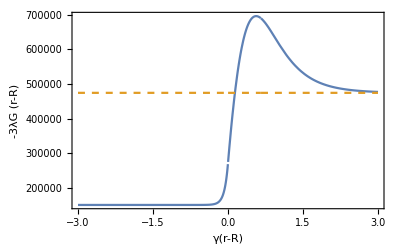

```mathematica
Plot[Evaluate[{-3 λ GField[χ[s/γ], χ[s/γ]], -3 λ GField[1-10^-5, 1-10^-5]}/.p->γ/.allParams], {s, -3, 3}/.allParams,Frame->True, FrameLabel->{"γ(r-R)", "-3λG (r-R)"}, PlotRange->All,  PlotStyle->{{}, {Dashed}}, LabelStyle->FontFamily->"ComputerModern", FrameStyle->Black]
```

## Tadpole Contribution

### Pseudo-Counterterms

```mathematica
Δλ[p_] :=(9 (p^2 π+3 (-5 √3+π) γ^2) λ^2)/(4 p^2 π (p^2+3 γ^2) √(p^2+4 γ^2))
Δm2[p_]:=-(3 (p^4 π+6 p^2 π γ^2+9 (-11 √3+π) γ^4) λ)/(2 p^2 π (p^2+3 γ^2) √(p^2+4 γ^2))
```

### Numerical Integration

#### Parameters

```mathematica
bins = 100;origin = 10^-5; infinity = 1-10^-5;pMin = 10^-2 γ/.allParams;
```

```mathematica
ΔχExt = (infinity - χ0)/bins/.allParams; ΔχInt = (χ0-origin)/bins/.allParams; Δx = (infinity - origin)/100/.allParams;xRange = Range[origin,infinity , Δx];
```

```mathematica
extχRange = Range[χ0/.allParams, infinity, ΔχExt]; intχRange = Range[origin, χ0/.allParams,ΔχInt ];
```

#### Exterior

```mathematica
extΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GPlusField[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->40], {χ, χ0/.allParams, infinity, ΔχExt}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
extData = Table[{extχRange[[n]], extΠVals[[n]]}, {n, 1, Length[extχRange]}];
```

```mathematica
extΠ = Interpolation[extData, InterpolationOrder->globalInterpolationOrder];
```

Interpolation::inord: Value of option InterpolationOrder -> globalInterpolationOrder should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 1.

#### Interior

```mathematica
intΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GMinusField[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->40], {χ, origin, χ0/.allParams, ΔχInt}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
intData = Table[{intχRange[[n]], intΠVals[[n]]}, {n, 1, Length[intχRange]}];
```

```mathematica
intΠ = Interpolation[intData];
```

#### Full

```mathematica
Π = Interpolation[Join[intData, Delete[extData,1]]];
```

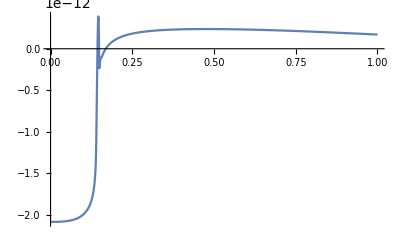

```mathematica
Plot[Evaluate[Π[χ]/.allParams], {χ,0,1}, PlotRange->All]
```

#### Relative Error

```mathematica
ExactΠ[χ_] := (9 λ γ^2)/(8 π^2) (6 + (1 - χ^2) (5 - π/(√3) χ^2));
```

```mathematica
ApproxΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GPlus1[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->30], {χ, χ0/.allParams, infinity, ΔχExt}];
```

```mathematica
ApproxΠData = Table[{extχRange[[n]], ApproxΠVals[[n]]}, {n, 1, Length[extχRange]}];
```

```mathematica
ApproxΠ = Interpolation[ApproxΠData]
```

InterpolatingFunction[…]

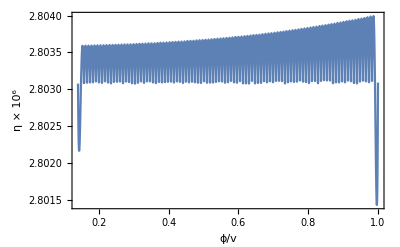

```mathematica
Plot[10^6 (Evaluate[ExactΠ[χ]/.allParams]- ApproxΠ[χ])/Evaluate[ExactΠ[χ]/.allParams], {χ, χ0, 1}/.allParams,Frame->True, FrameLabel->{"ϕ/v", "η × 10^6"}, LabelStyle->FontFamily->"ComputerModern", PlotRange->All, FrameStyle->Black]
```

## One-Loop Quantities

### Field

```mathematica
infinity=1;
```

```mathematica
δϕ1Vals = Table[NIntegrate[v/(γ (1 - y^2))(GFieldRest[x, y]) Π[y] y/.allParams, {y, χ0/.allParams, infinity}, Method->"GlobalAdaptive"], {x, origin, infinity, Δx}];
```

```mathematica
δϕ2Vals = Table[NIntegrate[v/(γ y √(g^2 + y^2))(GFieldRest[x, y]) Π[y] y/.allParams, {y, origin, χ0/.allParams}, Method->"GlobalAdaptive"], {x, origin, infinity, Δx}];
```

```mathematica
δϕData = Table[{xRange[[n]], (δϕ1Vals + δϕ2Vals)[[n]]}, {n, 1, Length[xRange]}];
```

```mathematica
δϕ = Interpolation[δϕData]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {9.64625×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

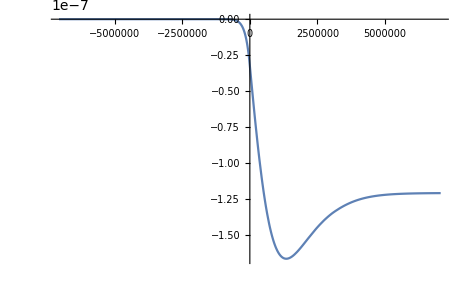

```mathematica
Plot[δϕ[χ[s]]/.allParams, {s, -5/γ, 5/γ}/.allParams, PlotRange->All]
```

```mathematica
ϕcl[s_] := v χ[s]/.allParams
```

```mathematica
ϕqu[s_] := v χ[s]+ δϕ[χ[s]]/.allParams
```

InterpolatingFunction::dmval: Input value {9.64625×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

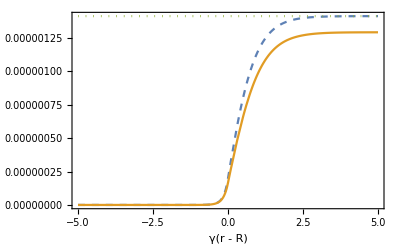

```mathematica
Plot[Evaluate[{ϕcl[s/γ],ϕqu[s/γ], v}/.allParams], {s, -5, 5}/.allParams, Frame->True, FrameLabel->{"γ(r - R)", "ϕ"}, PlotRange->All, LabelStyle->FontFamily->"ComputerModern", PlotStyle->{Dashed, {}, Dotted}, FrameStyle->Black]
```

InterpolatingFunction::dmval: Input value {9.64625×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

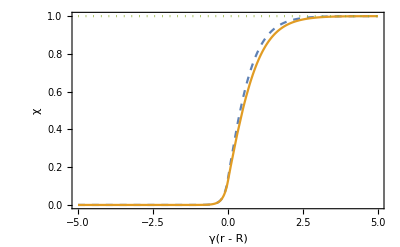

```mathematica
Plot[Evaluate[{ϕcl[s/γ]/v,ϕqu[s/γ]/(v (1 - (27 λ)/(16 π^2))), 1}/.allParams], {s, -5, 5}/.allParams, Frame->True, FrameLabel->{"γ(r - R)", "χ"}, PlotRange->All, LabelStyle->FontFamily->"ComputerModern", PlotStyle->{Dashed, {}, Dotted}, FrameStyle->Black]
```

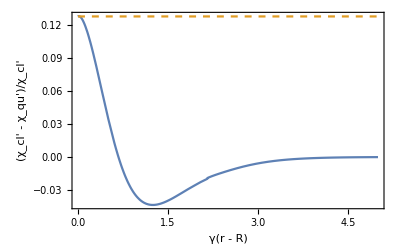

```mathematica
Plot[Evaluate[{(D[ϕcl[s/γ]/v, s]-D[ϕqu[s/γ]/(v (1 - (27 λ)/(16 π^2))), s])/Sech[ArcTanh[χ0]]^2, (81 λ)/(32 π^2)}/.allParams], {s, 0, 5}/.allParams, Frame->True, FrameLabel->{"γ(r - R)", "(χ_cl' - χ_qu')/χ_cl'"}, PlotRange->All, LabelStyle->FontFamily->"ComputerModern", FrameStyle->Black, PlotStyle->{{}, Dashed}]
```

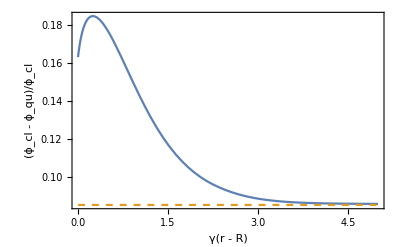

```mathematica
Plot[{Evaluate[(ϕcl[s/γ]-ϕqu[s/γ])/ϕcl[s/γ]/.allParams], 0.085}, {s, 0, 5}/.allParams, Frame->True, FrameLabel->{"γ(r - R)", "(ϕ_cl - ϕ_qu)/ϕ_cl"}, LabelStyle->FontFamily->"ComputerModern", FrameStyle->Black, PlotStyle->{{}, Dashed}, PlotRange->All]
```

### Acceleration

```mathematica
acl[s_] :=Evaluate[1/M^2 ϕcl[s] ϕcl'[s]]
```

```mathematica
aqu[s_]:=Evaluate[1/M^2(v χ[s] v χ'[s] + v χ[s] D[δϕ[χ[s]], s] + δϕ[χ[s]] v χ'[s])]
```

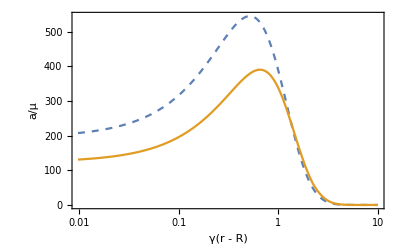

```mathematica
LogLinearPlot[Evaluate[10^23 {acl[s/γ]/μ, aqu[s/γ]/μ}/.allParams], {s, 0, 10}, PlotRange->All, Frame->True, FrameStyle->Black, FrameLabel->{"γ(r - R)", "a/μ"}, GridLines->{{1/2}, {}}, GridLinesStyle->Dashed, PlotStyle->{Dashed, {}}, LabelStyle->FontFamily->"ComputerModern"]
```

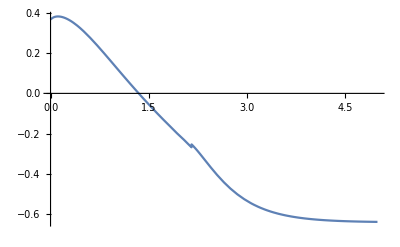

```mathematica
Plot[(acl[s/γ] - aqu[s/γ])/acl[s/γ]/.allParams, {s, 0, 5}]
```

## Parametric Dependence of Quantum Corrections

### λ-dependence

```mathematica
λdata = {};
```

```mathematica
λRange = Range[0.01, 1, 0.01];
```

```mathematica
Length[λRange]
```

100

```mathematica
For[i=1, i<Length[λRange]+1, i++,
λ = λRange[[i]];
extΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GPlusField[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->40], {χ, χ0/.allParams, infinity, ΔχExt}];
extData = Table[{extχRange[[n]], extΠVals[[n]]}, {n, 1, Length[extχRange]}];
extΠ = Interpolation[extData];
intΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GMinusField[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->40], {χ, origin, χ0/.allParams, ΔχInt}];
intData = Table[{intχRange[[n]], intΠVals[[n]]}, {n, 1, Length[intχRange]}];
intΠ = Interpolation[intData];
Π = Interpolation[Join[intData, Delete[extData,1]]];
δϕ1Vals = Table[NIntegrate[N[v/(γ (1 - y^2))(GField[x, y]/.p->pMin) Π[y] y/.allParams, 10], {y, χ0/.allParams, infinity}, Method->"GlobalAdaptive"], {x, origin, infinity, Δx}];
δϕ2Vals = Table[NIntegrate[N[v/(γ y √(g^2 + y^2))(GField[x, y]/.p->pMin) Π[y] y/.allParams, 10], {y, origin, χ0/.allParams}, Method->"GlobalAdaptive"], {x, origin, infinity, Δx}];
δϕData = Delete[Table[{xRange[[n]], (δϕ1Vals + δϕ2Vals)[[n]]}, {n, 1, Length[xRange]}], -1];
δϕ = Interpolation[δϕData];
classicalForce[s_] :=Evaluate[1/M^2 v χ[s] v χ'[s]];
quantumForce[s_]:=Evaluate[1/M^2 (v χ[s] + δϕ[χ[s]]) D[v χ[s] + δϕ[χ[s]], s]];
λdata = Join[λdata, {100 ((classicalForce[s] - quantumForce[s])/classicalForce[s]/.s->1/(2 γ)/.allParams)}];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

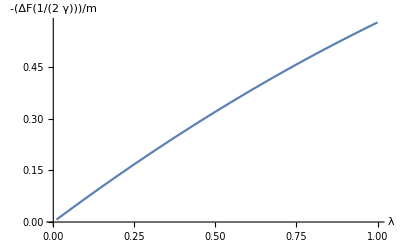

```mathematica
ListLinePlot[Table[{λRange[[n]], 1/100 λdata[[n]]}, {n, 1, Length[λRange]}], PlotRange->Full, AxesLabel->{"λ", -ΔF[1/(2 γ)]/m}, LabelStyle->FontFamily->"ComputerModern"]
```

### μ-dependence

```mathematica
μdata = {};
```

```mathematica
μRange = Table[10^k, {k, -2, 0, .1}];
```

```mathematica
Length[μRange]
```

21

```mathematica
For[i=1, i<Length[μRange]+1, i++,
μ = μRange[[i]];
extΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GPlusField[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->40], {χ, χ0/.allParams, infinity, ΔχExt}];
extData = Table[{extχRange[[n]], extΠVals[[n]]}, {n, 1, Length[extχRange]}];
extΠ = Interpolation[extData];
intΠVals = Table[1/(2 π^2) NIntegrate[γ p^2/k(-3 λ GMinusField[χ, χ] + Δm2[p]+ Δλ[p] (2 γ^2)/λ χ^2)/.p->γ Log[1/k]/.allParams, {k,0,1}, Method->"GlobalAdaptive", MaxRecursion->40], {χ, origin, χ0/.allParams, ΔχInt}];
intData = Table[{intχRange[[n]], intΠVals[[n]]}, {n, 1, Length[intχRange]}];
intΠ = Interpolation[intData];
Π = Interpolation[Join[intData, Delete[extData,1]]];
δϕ1Vals = Table[NIntegrate[N[v/(γ (1 - y^2))(GField[x, y]/.p->pMin) Π[y] y/.allParams, 10], {y, χ0/.allParams, infinity}, Method->"GlobalAdaptive"], {x, origin, infinity, Δx}];
δϕ2Vals = Table[NIntegrate[N[v/(γ y √(g^2 + y^2))(GField[x, y]/.p->pMin) Π[y] y/.allParams, 10], {y, origin, χ0/.allParams}, Method->"GlobalAdaptive"], {x, origin, infinity, Δx}];
δϕData = Delete[Table[{xRange[[n]], (δϕ1Vals + δϕ2Vals)[[n]]}, {n, 1, Length[xRange]}], -1];
δϕ = Interpolation[δϕData];
classicalForce[s_] :=Evaluate[1/M^2 v χ[s] v χ'[s]];
quantumForce[s_]:=Evaluate[1/M^2(v χ[s] v χ'[s] + v χ[s] D[δϕ[χ[s]], s] + δϕ[χ[s]] v χ'[s])];
μdata = Join[μdata, {100 ((classicalForce[s] - quantumForce[s])/classicalForce[s]/.s->1/(2 γ)/.allParams)}];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

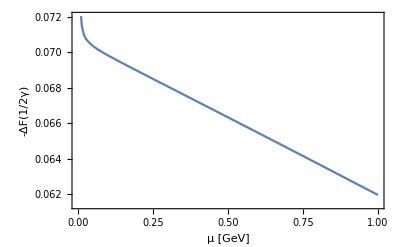

```mathematica
ListLinePlot[Table[{μRange[[n]], 1/100 μdata[[n]]}, {n, 1, Length[μdata]}], Frame->True, FrameLabel->{"μ [GeV]", "-ΔF(1/2γ)"}, FrameStyle->Black, LabelStyle->FontFamily->"ComputerModern"]
```